```mathematica
<<KerrGeodesics`
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
a=.998`32;
r0 = 10`32;
x = Cos[π/4`32];
Freqs=KerrGeoFrequencies[a,r0,0,x];
Ωθ=Freqs[[2]];
Ωϕ= Freqs[[3]];
orbit = KerrGeoOrbit[a,r0,0,x];
{t,r,θ,ϕ} = orbit["Trajectory"];
Υ = orbit["Frequencies"]["Υ_θ"];
Υϕ = orbit["Frequencies"]["Υ_ϕ"];
ℰ=orbit["Energy"];
ℒ=orbit["AngularMomentum"];
```

```mathematica
l=3;
m=1;
k=3;
dtdλ[θ_]:= ℰ(((r0^2+a^2)^2)/(r0^2-2 r0+a^2)-a^2 Sin[θ]^2)+a ℒ(1-(r0^2+a^2)/(r0^2-2r0 +a^2))
ω = m Ωϕ + k Ωθ;

ut[θ_]:=-(4 a r0 ℒ)/((a^2+(-2+r0) r0) (a^2+2 r0^2+a^2 Cos[2 θ]))+(ℰ (a^4+2 r0^4+a^2 r0 (2+3 r0)+a^2 (a^2+(-2+r0) r0) Cos[2 θ]))/((a^2+(-2+r0) r0) (a^2+2 r0^2+a^2 Cos[2 θ]))

S = Table[SpinWeightedSpheroidalHarmonicS[0,l,m,a (m Ωϕ+k Ωθ)],{l,0,5},{m,-l,l},{k,-5,5}];
```

```mathematica
l=3;
m=1;
k=5;

T = -(2 Ωθ r0)/(r0^2-2 r0 +a^2)Table[NIntegrate[S[[l+1,l+m+1,6+k]][θ[λ],0]Cos[m(Ωϕ t[λ]-ϕ[λ])+k Ωθ t[λ]]dtdλ[λ],{λ,0,(2π)/Υ},Method->"Trapezoidal",PrecisionGoal->10],{k,-5,5}];
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in λ in the region {{0.,1.78664}}. NIntegrate obtained 0.000657176 and 6.47257×10^-9 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in λ in the region {{0.,1.78664}}. NIntegrate obtained 6.33547 and 6.47338×10^-9 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in λ in the region {{0.,1.78664}}. NIntegrate obtained -0.00657439 and 6.47396×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvi will be suppressed during this calculation.

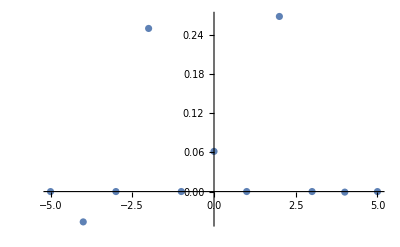

```mathematica
ListPlot[Thread[{Table[k,{k,-5,5}],T}](*,PlotRange->{-.0001,.0001}*)]
```

```mathematica
-(2 Ωθ r0)/(r0^2-2 r0 +a^2)
```

-0.00731737683093819233411150895